```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Options[ReadODR]:={"Plot"->True};
ReadODR[fn_,OptionsPattern[]]:=Module[{tmp,tmp2,data,timels,outmat},
data=Import[fn];
tmp=StringSplit[data," "];
timels=Table[i/100.,{i,1,Length@tmp}];
tmp2=Table[StringSplit[tmp[[i]],","]//ToExpression,{i,Length@tmp}];
outmat=tmp2ᵀ;
If[OptionValue["Plot"],
ListPlot[Thread[{timels,#}]&/@outmat,Joined->True,Frame->True,GridLines->Automatic,FrameLabel->{"time (min)","Response"},PlotRange->{0,Automatic},LabelStyle->Directive[Bold, Medium,FontFamily->"Times New Roman"],PlotLegends->LineLegend[{"1","2","3","4"},LegendLabel->"Sensor",LegendFunction->Framed]],
Return[tmp2ᵀ]
]
];
```

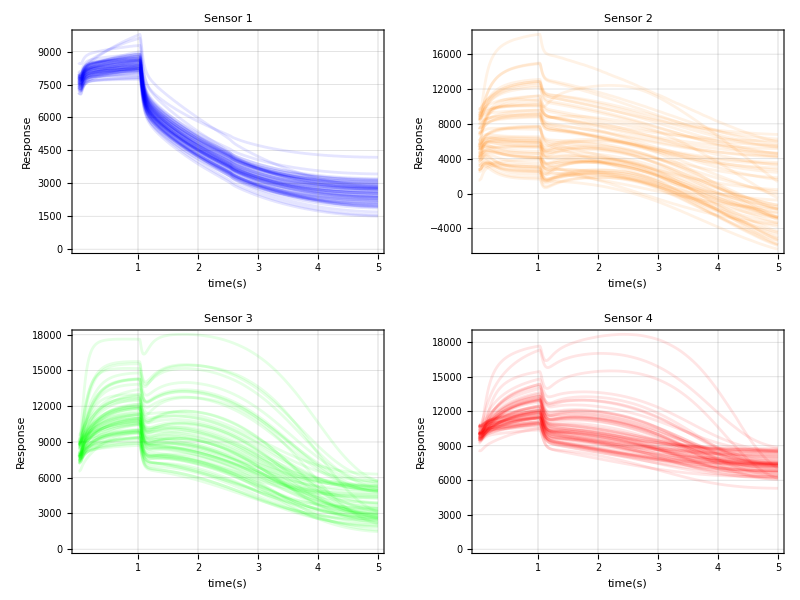
-Graphics-Dengue

```mathematica
Colors={1->Blue,2->Orange,3->Green,4->Red};
Labeled[Grid[Partition[Table[ListPlot[[[j]],PlotStyle->{Opacity[0.1,j/.Colors]},Joined->True,Frame->True,GridLines->Automatic,PlotRange->Full,FrameLabel->{"time(s)","Response"},FrameTicks->{{Automatic,None},{Table[{i,i/100},{i,{100,200,300,400,500}}],None}},PlotLabel->"Sensor "<>ToString@j,ImageSize->Medium],{j,1,4}],2],Frame->All],Style["Dengue", 18,Bold],Top]
```

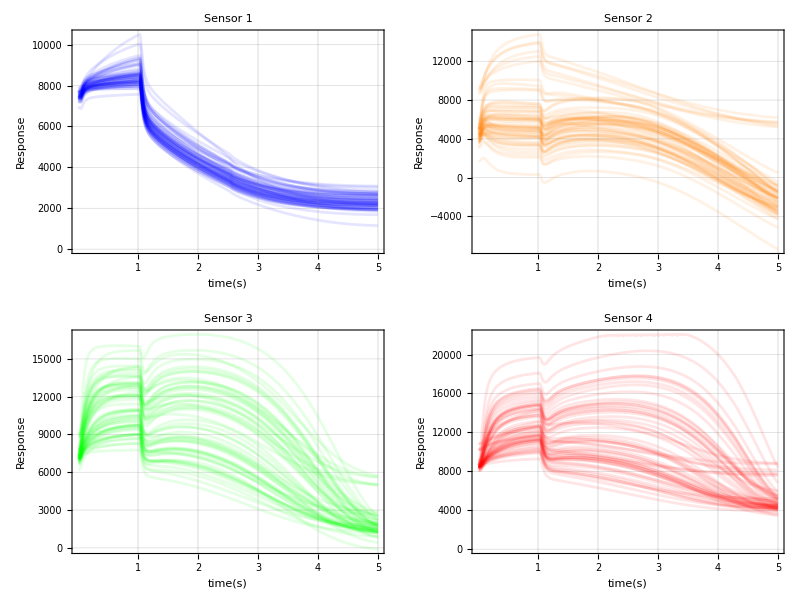
-Graphics-Healthy

```mathematica
Colors={1->Blue,2->Orange,3->Green,4->Red};
Labeled[Grid[Partition[Table[ListPlot[[[j]],PlotStyle->{Opacity[0.1,j/.Colors]},Joined->True,Frame->True,GridLines->Automatic,PlotRange->Full,FrameLabel->{"time(s)","Response"},FrameTicks->{{Automatic,None},{Table[{i,i/100},{i,{100,200,300,400,500}}],None}},PlotLabel->"Sensor "<>ToString@j,ImageSize->Medium],{j,1,4}],2],Frame->All],Style["Healthy", 18,Bold],Top]
```

```mathematica
(*โหลดข้อมูลในไดเรกตอรี และเก็บเป็นลิสต์ของข้อมูลจากแต่ละไฟล์*)
loadData[dir_]:=Module[{files,validFiles,dataList},files=FileNames["*",dir];
validFiles=Select[files,FileNameTake[#]=!=".DS_Store"&];
dataList=StringSplit/@(Import[#,"Text"]&/@validFiles);
{dataList,validFiles}]


(*ลดขนาดข้อมูลให้เหลือ 5 จุดตัวอย่างต่อเซนเซอร์ normalize ด้วยค่าสัญญาณที่ time point 100 แล้วเก็บเป็น {5,4}*)
makeFeature[datas_]:=Module[{FDatas={},datays,norm,datay1,datay2,datay3,fdatas},datays=ToExpression/@StringSplit[datas[[100]],","];
norm=datays;
AppendTo[FDatas,norm];
datays=ToExpression/@StringSplit[datas[[200]],","];
datay1=datays;
fdatas={(datays[[1]]-norm[[1]])/norm[[1]],(datays[[2]]-norm[[2]])/norm[[2]],(datays[[3]]-norm[[3]])/norm[[3]],(datays[[4]]-norm[[4]])/norm[[4]]};
AppendTo[FDatas,fdatas];
datays=ToExpression/@StringSplit[datas[[300]],","];
datay2=datays;
fdatas={(datays[[1]]-datay1[[1]])/norm[[1]],(datays[[2]]-datay1[[2]])/norm[[2]],(datays[[3]]-datay1[[3]])/norm[[3]],(datays[[4]]-datay1[[4]])/norm[[4]]};
AppendTo[FDatas,fdatas];
datays=ToExpression/@StringSplit[datas[[400]],","];
datay3=datays;
fdatas={(datays[[1]]-datay2[[1]])/norm[[1]],(datays[[2]]-datay2[[2]])/norm[[2]],(datays[[3]]-datay2[[3]])/norm[[3]],(datays[[4]]-datay2[[4]])/norm[[4]]};
AppendTo[FDatas,fdatas];
datays=ToExpression/@StringSplit[datas[[500]],","];
fdatas={(datays[[1]]-datay3[[1]])/norm[[1]],(datays[[2]]-datay3[[2]])/norm[[2]],(datays[[3]]-datay3[[3]])/norm[[3]],(datays[[4]]-datay3[[4]])/norm[[4]]};
AppendTo[FDatas,fdatas];
FDatas]


(*ทำ feature extraction ให้ทุกตัวอย่างใน list*)
getFeatureList[dataList_]:=Module[{FList},FList=makeFeature/@dataList;
FList]


(*คำนวณผลต่างอันดับหนึ่ง*)
get1stOrderFeature[datas_,id_]:=Module[{fdata,makeY,datay1,datay2,datay3,datay4,datay5,datax},fdata=datas[[id]];
makeY[col_]:={fdata[[1,col]]/1000-fdata[[1,col]]/1000,fdata[[2,col]]*20-fdata[[1,col]]/1000,fdata[[3,col]]*20-fdata[[1,col]]/1000,fdata[[4,col]]*20-fdata[[1,col]]/1000,fdata[[5,col]]*20-fdata[[1,col]]/1000};
datay1=makeY[1];
datay2=makeY[2];
datay3=makeY[3];
datay4=makeY[4];
datay5=Join[datay1,datay2+datay1[[5]],datay3+datay1[[5]]+datay2[[5]],datay4+datay1[[5]]+datay2[[5]]+datay3[[5]]];
datax=Range[0,Length[datay5]-1];
{datax,datay5}]


(*คำนวณผลต่างอันดับสอง*)
get2ndOrderFeature[datas_,id_]:=Module[{fdata,makeY,datay1,datay2,datay3,datay4,datay5,datay6,norm,datax},fdata=datas[[id]];
makeY[col_]:={fdata[[1,col]]/1000-fdata[[1,col]]/1000,fdata[[2,col]]*20-fdata[[1,col]]/1000,fdata[[3,col]]*20-fdata[[1,col]]/1000,fdata[[4,col]]*20-fdata[[1,col]]/1000,fdata[[5,col]]*20-fdata[[1,col]]/1000};
datay1=makeY[1];
datay2=makeY[2];
datay3=makeY[3];
datay4=makeY[4];
datay5=Join[datay1,datay2+datay1[[5]],datay3+datay1[[5]]+datay2[[5]],datay4+datay1[[5]]+datay2[[5]]+datay3[[5]]];
norm=datay5[[2]]-datay5[[1]];
datay6=Differences[datay5]-norm;
datax=Range[0,Length[datay6]-1];
{datax,datay6}]
```

```mathematica
{DenguerawData,DenguefileList}=;
```

```mathematica
{NormalrawData,NormalfileList}=;
```

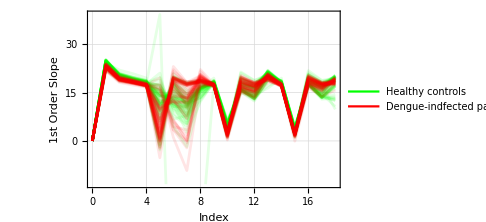

```mathematica
Show[
ListLinePlot[Table[Transpose[get2ndOrderFeature[getFeatureList[NormalrawData],i]],{i,Length@NormalfileList}],Frame->True,PlotStyle->Opacity[0.1,Green],GridLines->Automatic,FrameLabel->{"Index", "1st Order Slope"},LabelStyle->Directive[Bold, Medium,FontFamily->"Merriweather Sans"],PlotLegends->LineLegend[{Green},{"Healthy controls"}],ImageSize->Medium],
ListLinePlot[Table[Transpose[get2ndOrderFeature[getFeatureList[DenguerawData],i]],{i,Length@DenguefileList}],Frame->True,PlotStyle->Opacity[0.1,Red],GridLines->Automatic,PlotLegends->LineLegend[{Red},{"Dengue-indfected patients"}],LabelStyle->Directive[Bold, Medium,FontFamily->"Merriweather Sans"],ImageSize->Medium]
]
```

```mathematica
FNormal=getFeatureList[NormalrawData];
FDengue=getFeatureList[DenguerawData];
FIgG=getFeatureList[IgGrawData];

normal2nd=Table[get2ndOrderFeature[FNormal,i][[2]],{i,Length[FNormal]}];
dengue2nd=Table[get2ndOrderFeature[FDengue,i][[2]],{i,Length[FDengue]}];
igg2nd=Table[get2ndOrderFeature[FIgG,i][[2]],{i,Length[FIgG]}];


NId=normal2nd[[All,12]]-normal2nd[[All,11]];
NClassified=normal2nd[[All,10]]-normal2nd[[All,9]];

DId=dengue2nd[[All,12]]-dengue2nd[[All,11]];
DClassified=dengue2nd[[All,10]]-dengue2nd[[All,9]];

IgId=igg2nd[[All,12]]-igg2nd[[All,11]];
IgClassified=igg2nd[[All,10]]-igg2nd[[All,9]];
```

```mathematica
normalPoints=Transpose[{NId,NClassified}];
denguePoints=Transpose[{DId,DClassified}];
iggPoints=Transpose[{IgId,IgClassified}];
```

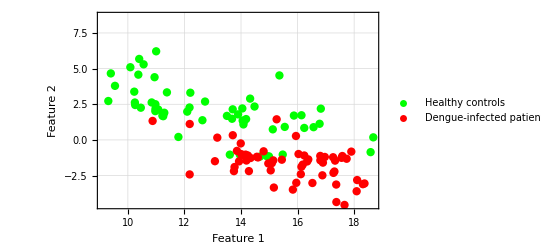

```mathematica
ListPlot[{normalPoints,denguePoints},Frame->True,FrameLabel->{"Feature 1", "Feature 2"},PlotStyle->{{Green,PointSize[0.015]},{Red,PointSize[0.015]},{Brown,PointSize[0.015]}},GridLines->Automatic,LabelStyle->Directive[Bold, Medium,FontFamily->"Merriweather Sans"],PlotLegends->{"Healthy controls","Dengue-infected patients"}]
```

```mathematica
AllData=Join[Thread[normalPoints->"Healthy"],Thread[denguePoints->"Dengue"]];
```

## Logistic Regression

```mathematica
SeedRandom[12345];
val=[AllData,Function[Classify[#,Method->"LogisticRegression"]],Method->{"KFold","Folds"->5,"Runs"->4}];
```

```mathematica
<|"Accuracy"->Mean@Table[val[[i,"ValidationResult"]]["Accuracy"],{i,1,Length@val}],
"SD"->StandardDeviation@Table[val[[i,"ValidationResult"]]["Accuracy"],{i,1,Length@val}]
|>
```

<|Accuracy→0.885779,SD→0.0468863|>

```mathematica
<|"Precision"->Mean@Table[val[[i,"ValidationResult"]]["Precision"],{i,1,Length@val}],
"SD"->StandardDeviation@Table[val[[i,"ValidationResult"]]["Precision"],{i,1,Length@val}]
|>
```

<|Precision→<|Dengue→0.870522,Healthy→0.899602|>,SD→<|Dengue→0.0715988,Healthy→0.0789092|>|>

```mathematica
<|"Sensitivity"->Mean@Table[val[[i,"ValidationResult"]]["Sensitivity"],{i,1,Length@val}],
"SD"->StandardDeviation@Table[val[[i,"ValidationResult"]]["Sensitivity"],{i,1,Length@val}]
|>
```

<|Sensitivity→<|Dengue→0.905587,Healthy→0.869285|>,SD→<|Dengue→0.0731702,Healthy→0.0542908|>|>

```mathematica
<|"Recall"->Mean@Table[val[[i,"ValidationResult"]]["Recall"],{i,1,Length@val}],
"SD"->StandardDeviation@Table[val[[i,"ValidationResult"]]["Recall"],{i,1,Length@val}]
|>
```

<|Recall→<|Dengue→0.905587,Healthy→0.869285|>,SD→<|Dengue→0.0731702,Healthy→0.0542908|>|>

```mathematica
<|"Specificity"->Mean@Table[val[[i,"ValidationResult"]]["Specificity"],{i,1,Length@val}],
"SD"->StandardDeviation@Table[val[[i,"ValidationResult"]]["Specificity"],{i,1,Length@val}]
|>
```

<|Specificity→<|Dengue→0.869285,Healthy→0.905587|>,SD→<|Dengue→0.0542908,Healthy→0.0731702|>|>

```mathematica
<|"AreaUnderROCCurve"->Mean@Table[val[[i,"ValidationResult"]]["AreaUnderROCCurve"],{i,1,Length@val}],
"SD"->StandardDeviation@Table[val[[i,"ValidationResult"]]["AreaUnderROCCurve"],{i,1,Length@val}]
|>
```

<|AreaUnderROCCurve→<|Dengue→0.945726,Healthy→0.945726|>,SD→<|Dengue→0.0300497,Healthy→0.0300497|>|>

```mathematica
rocs=Table[val[[i,"ValidationResult"]]["ROCData"]["Dengue"]["ROCPoint"],{i,Length@val}];
(*Clean one ROC curve:if the same FPR appears multiple times,keep the highest TPR at that FPR*)
cleanROC[roc_]:=Values[Last/@GroupBy[roc,First]]
cleanedROCs=cleanROC/@rocs;
fprGrid=Range[0,1,0.01];
(*Interpolate each cleaned ROC*)
interp=Interpolation[#,InterpolationOrder->1]&/@cleanedROCs;
(*Sample all curves on the same grid*)
tprMatrix=Table[interp[[k]]/@fprGrid,{k,Length[interp]}];
(*Mean ROC*)
meanTPR=Mean/@Transpose[tprMatrix];
meanROC=Transpose[{fprGrid,meanTPR}];
```

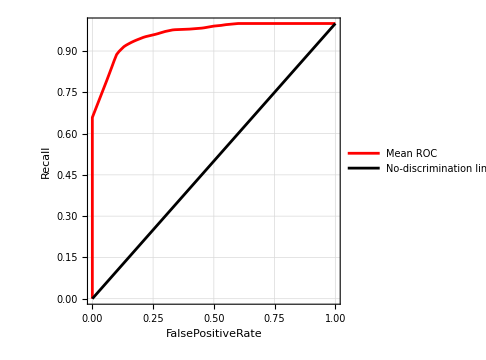

```mathematica
rocplot=ListLinePlot[{{{0,0}}~Join~meanROC,Table[{x,x},{x,0,1,0.01}]},PlotStyle->{Red,Black},Frame->True,FrameLabel->{"FalsePositiveRate","Recall"},PlotLegends->{"Mean ROC","No-discrimination line"},AspectRatio->1,GridLines->Automatic,LabelStyle->Directive[Bold, Medium,FontFamily->"Merriweather Sans"],ImageSize->Medium]
```

```mathematica
Total@Table[val[[i,"ValidationResult"]]["ConfusionMatrix"],{i,Length@val}]
```

{{217,23,0},{31,201,0}}

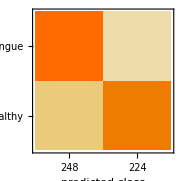
Classifier Measurements
Number of test examples | 472
Accuracy | (88.61.5) %
Accuracy baseline | (50.82.3) %
-Graphics- |

```mathematica
cm=[Total@Table[val[[i,"ValidationResult"]]["ConfusionMatrix"],{i,Length@val}],{"Dengue","Healthy"}]
```

```mathematica
Grid[{{rocplot, Rasterize[cm["ConfusionMatrixPlot"],"Image",ImageSize->Medium]}},Frame->All]
```

-Graphics- | -Graphics-

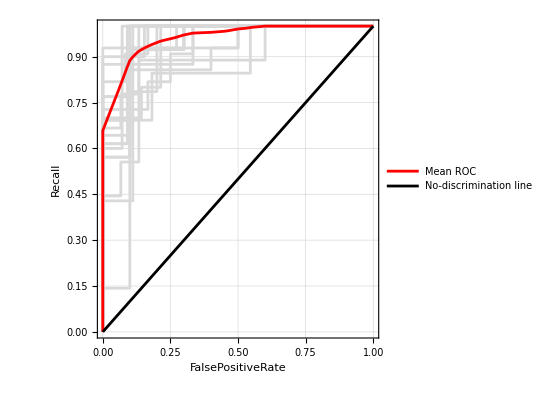

```mathematica
Show[
ListPlot[Table[val[[i,"ValidationResult"]]["ROCData"]["Dengue"]["ROCPoint"],{i,Length@val}],Joined->True,PlotStyle->LightGray,Frame->True,FrameLabel->{"FalsePositiveRate","Recall"},AspectRatio->1,GridLines->Automatic,LabelStyle->Directive[Bold, Medium,FontFamily->"Merriweather Sans"]],

ListLinePlot[{{{0,0}}~Join~meanROC,Table[{x,x},{x,0,1,0.01}]},PlotStyle->{Red,Black},Frame->True,FrameLabel->{"FalsePositiveRate","Recall"},PlotLegends->{"Mean ROC","No-discrimination line"},AspectRatio->1,GridLines->Automatic,LabelStyle->Directive[Bold, Medium,FontFamily->"Merriweather Sans"]]

]
```

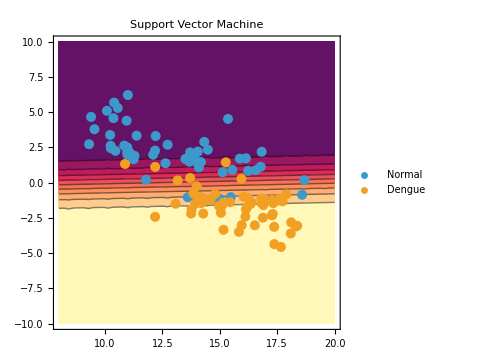

```mathematica
tmp=val[[1,"FittedModel"]];
	lrg=Quiet@ContourPlot[tmp[{x,y},"Probabilities"]["Dengue"],{x,8,20},{y,-10,10}];
Show[lrg,ListPlot[{normalPoints,denguePoints},PlotStyle->{PointSize[0.02]},PlotLegends->{"Normal","Dengue"}],PlotLabel->"Support Vector Machine",ImageSize->Medium]
```

## Support Vector Machine

```mathematica
valsvm=[AllData,Function[Classify[#,Method->"SupportVectorMachine"]],Method->{"KFold","Folds"->5}];
```

```mathematica
<|"Accuracy"->Mean@Table[valsvm[[i,"ValidationResult"]]["Accuracy"],{i,1,5}],
"SD"->StandardDeviation@Table[valsvm[[i,"ValidationResult"]]["Accuracy"],{i,1,5}]
|>
```

<|Accuracy→0.864493,SD→0.0615062|>

```mathematica
<|"Precision"->Mean@Table[valsvm[[i,"ValidationResult"]]["Precision"],{i,1,5}],
"SD"->StandardDeviation@Table[valsvm[[i,"ValidationResult"]]["Precision"],{i,1,5}]
|>
```

<|Precision→<|Dengue→0.853014,Normal→0.873333|>,SD→<|Dengue→0.0721157,Normal→0.140732|>|>

```mathematica
<|"Sensitivity"->Mean@Table[valsvm[[i,"ValidationResult"]]["Sensitivity"],{i,1,5}],
"SD"->StandardDeviation@Table[valsvm[[i,"ValidationResult"]]["Sensitivity"],{i,1,5}]
|>
```

<|Sensitivity→<|Dengue→0.897143,Normal→0.845263|>,SD→<|Dengue→0.103707,Normal→0.0636312|>|>

```mathematica
<|"Recall"->Mean@Table[valsvm[[i,"ValidationResult"]]["Recall"],{i,1,5}],
"SD"->StandardDeviation@Table[valsvm[[i,"ValidationResult"]]["Recall"],{i,1,5}]
|>
```

<|Recall→<|Dengue→0.897143,Normal→0.845263|>,SD→<|Dengue→0.103707,Normal→0.0636312|>|>

```mathematica
<|"Specificity"->Mean@Table[valsvm[[i,"ValidationResult"]]["Specificity"],{i,1,5}],
"SD"->StandardDeviation@Table[valsvm[[i,"ValidationResult"]]["Specificity"],{i,1,5}]
|>
```

<|Specificity→<|Dengue→0.845263,Normal→0.897143|>,SD→<|Dengue→0.0636312,Normal→0.103707|>|>

```mathematica
<|"AreaUnderROCCurve"->Mean@Table[valsvm[[i,"ValidationResult"]]["AreaUnderROCCurve"],{i,1,5}],
"SD"->StandardDeviation@Table[valsvm[[i,"ValidationResult"]]["AreaUnderROCCurve"],{i,1,5}]
|>
```

<|AreaUnderROCCurve→<|Dengue→0.947885,Normal→0.947885|>,SD→<|Dengue→0.0364644,Normal→0.0364644|>|>

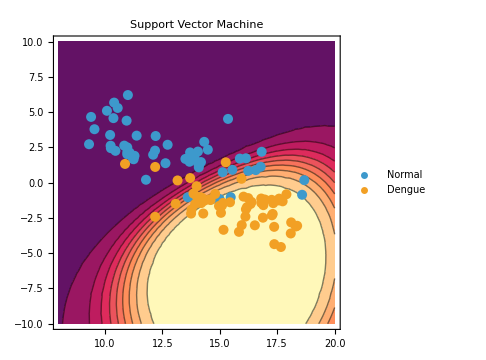

```mathematica
tmp=valsvm[[1,"FittedModel"]];
svm=Quiet@ContourPlot[tmp[{x,y},"Probabilities"]["Dengue"],{x,8,20},{y,-10,10}];
Show[svm,ListPlot[{normalPoints,denguePoints},PlotStyle->{PointSize[0.02]},PlotLegends->{"Normal","Dengue"}],PlotLabel->"Support Vector Machine",ImageSize->Medium]
```